```mathematica
aws=ServiceConnect["AWS"];
```

```mathematica
s3=ServiceExecute[aws,"GetService","Name"->"S3"];
```

```mathematica
braket=ServiceExecute[aws,"GetService","Name"->"Braket"];
```

```mathematica
braket
```

ServiceObject[…]

Fetch available devices:

```mathematica
devices=braket["SearchDevices","Filters"->{},"RequestRegion"->"us-east-1"]
```

```mathematica
braket["SearchDevices","Filters"->{},"RequestRegion"->"us-east-1"]
```

```mathematica
braket["SearchDevices","Filters"->{},"RequestRegion"->"us-west-2"]
```

QPU devices:

```mathematica
devices["Devices",Select[#DeviceType=="QPU"&]]
```

Query device:

```mathematica
devices["Devices",First@*Select[#DeviceName=="Aquila"&]][MapAt[ImportString[#,"RawJSON"]&,"DeviceCapabilities"]]
```

```mathematica
devices["Devices",First@*Select[#DeviceName=="IonQ Device"&]][MapAt[ImportString[#,"RawJSON"]&,"DeviceCapabilities"]]
```

```mathematica
deviceARN="arn:aws:braket:::device/qpu/rigetti/Aspen-11";
```

```mathematica
simDeviceARN="arn:aws:braket:::device/quantum-simulator/amazon/tn1";
```

Example qasm:

```mathematica
qasm="
// ghz.qasm
// Prepare a GHZ state
OPENQASM 3;

qubit[3] q;
bit[3] c;

h q[0];
cnot q[0], q[1];
cnot q[1], q[2];

c = measure q;";
```

This one doesn’t work, control modifiers are not supported and probably gates should be from the list of supported ones and not U:

```mathematica
qasm=QuantumCircuitOperator[{QuantumOperator["H",{1}],QuantumOperator["CNOT",{1,2}],QuantumOperator["CNOT",{2,3}],QuantumMeasurementOperator[{1,2,3}]}]["QASM"]
```

OPENQASM 3.0;
qubit[3] q;
bit[3] c;
U(pi/2, 0, pi) q[0];
ctrl(1) @ negctrl(0) @ U(pi, 0, pi) q[0] q[1];
ctrl(1) @ negctrl(0) @ U(pi, 0, pi) q[1] q[2];
c[0] = measure q[0];
c[1] = measure q[1];
c[2] = measure q[2];

Qiskit qasm needs some retouching, but works:

```mathematica
QuantumCircuitOperator[{QuantumOperator["H",{1}],QuantumOperator["CNOT",{1,2}],QuantumOperator["CNOT",{2,3}],QuantumMeasurementOperator[{1,2,3}]}]
```

QuantumCircuitOperator[…]

```mathematica
qasm=StringReplace[StringDelete[QuantumCircuitOperator[{QuantumOperator["H",{1}],QuantumOperator["CNOT",{1,2}],QuantumOperator["CNOT",{2,3}],QuantumMeasurementOperator[{1,2,3}]}]["Qiskit"]["QASM"],"include \"qelib1.inc\";"],"cx"->"cnot"]
```

OPENQASM 2.0;

qreg q[3];
creg c[3];
h q[0];
cnot q[0],q[1];
cnot q[1],q[2];
measure q[0] -> c[0];
measure q[1] -> c[2];
measure q[2] -> c[1];

```mathematica
QuantumOperator[{"RY",π/4}]["ZYZ"]==QuantumOperator[{"RY",π/4}]
```

True

```mathematica
qasm=StringReplace[StringDelete[QuantumCircuitOperator[{QuantumOperator[{"RY",π/4}],QuantumMeasurementOperator[]}]["Qiskit"]["QASM"],"include \"qelib1.inc\";"],"pi/4"->ToString[Pi/4.]]
```

OPENQASM 2.0;

qreg q[1];
creg c[1];
ry(0.785398) q[0];
measure q[0] -> c[0];

Create a task, replace DeviceArn for a different device:

```mathematica
task=braket["CreateQuantumTask",
"DeviceArn"->deviceARN,
"DeviceParameters"->{},
"OutputS3Bucket"->"amazon-braket-wolfram","OutputS3KeyPrefix"->"tasks",
"Shots"->100,"Action"-><|"braketSchemaHeader"-><|"name"->"braket.ir.openqasm.program","version"->"1"|>,"source"->qasm|>,"ValidateRequest"->False,"RequestRegion"->"us-west-1"]
```

List tasks:

```mathematica
braket["SearchQuantumTasks","Filters"->{},"RequestRegion"->"us-west-1"]["QuantumTasks"]
```

Get detailed information on a task:

```mathematica
braket["GetQuantumTask","QuantumTaskArn"->task["QuantumTaskArn"],"RequestRegion"->"us-west-1"]
```

Results are saved in S3

```mathematica
outputPath=braket["GetQuantumTask","QuantumTaskArn"->task["QuantumTaskArn"],"RequestRegion"->"us-west-1"]["OutputS3Directory"]
```

tasks/49be0e57-8a60-48d3-b038-7128d78b497d

This is the output from QPU device task:

```mathematica
outputPath="tasks/51185477-9f2d-4fe1-b08a-efc37db0996a";
```

```mathematica
results=ImportByteArray[s3["GetObject","Bucket"->"amazon-braket-wolfram","Key"->FileNameJoin[{outputPath,"results.json"}],"RequestRegion"->"us-west-1"]["Body"],"RawJSON"]
```

<|braketSchemaHeader→<|name→braket.task_result.gate_model_task_result,version→1|>,measurements→{{0,0,1},{1,0,1},{0,0,1},{1,1,1},{0,0,0},{1,1,0},{0,0,1},{1,1,1},{1,1,1},{0,0,0},{0,0,1},{0,1,0},{0,0,1},{1,0,1},{1,1,1},{1,1,0},{0,0,0},{0,0,0},{0,0,0},{0,0,1},{1,1,1},{0,0,0},{1,1,0},{0,0,1},{1,1,1},{0,0,0},{1,1,0},{1,1,0},{0,0,1},{1,1,1},{0,0,1},{0,0,1},{1,0,1},{1,1,1},{1,0,0},{1,1,0},{0,0,0},{1,1,1},{0,0,1},{0,1,1},{1,1,1},{0,0,0},{1,1,1},{1,0,0},{1,0,0},{0,0,0},{1,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{0,0,1},{1,0,1},{0,0,0},{0,0,0},{0,0,0},{1,1,1},{1,1,0},{1,1,1},{0,0,1},{0,0,1},{1,0,0},{1,0,1},{1,0,1},{1,1,0},{1,0,0},{0,0,0},{0,0,1},{1,1,1},{0,0,1},{0,0,0},{0,0,0},{1,1,0},{1,1,0},{1,1,1},{0,0,0},{1,0,0},{0,0,1},{1,1,1},{0,0,0},{1,0,0},{1,1,1},{1,1,1},{1,1,1},{1,0,1},{1,1,0},{1,1,1},{1,0,1},{0,0,1},{1,1,1},{1,0,0},{1,1,1},{0,0,0},{0,1,0},{0,1,1},{0,0,1},{1,1,1},{0,0,0},{1,0,1},{1,1,0}},resultTypes→{},measuredQubits→{0,1,2},taskMetadata→<|braketSchemaHeader→<|name→braket.task_result.task_metadata,version→1|>,id→arn:aws:braket:us-west-1:186494141299:quantum-task/49be0e57-8a60-48d3-b038-7128d78b497d,shots→100,deviceId→arn:aws:braket:::device/qpu/rigetti/Aspen-11,deviceParameters→<|braketSchemaHeader→<|name→braket.device_schema.rigetti.rigetti_device_parameters,version→1|>,paradigmParameters→<|braketSchemaHeader→<|name→braket.device_schema.gate_model_parameters,version→1|>,qubitCount→3,disableQubitRewiring→False|>|>,createdAt→2022-07-15T16:29:31.732Z,endedAt→2022-07-15T16:29:36.844Z,status→COMPLETED|>,additionalMetadata→<|action→<|braketSchemaHeader→<|name→braket.ir.openqasm.program,version→1|>,source→OPENQASM 2.0;

qreg q[3];
creg c[3];
h q[0];
cnot q[0],q[1];
cnot q[1],q[2];
measure q[0] -> c[2];
measure q[1] -> c[1];
measure q[2] -> c[0];
|>,rigettiMetadata→<|braketSchemaHeader→<|name→braket.task_result.rigetti_metadata,version→1|>,nativeQuilMetadata→<|finalRewiring→{35,36,37,0,1,2,3,4,5,6,7,10,11,12,13,14,15,16,17,20,21,22,23,24,25,26,27,30,31,32,33,34,42,43,44,45,46,47,8,9,18,19,28,29,38,39,40,41},gateDepth→15,gateVolume→20,multiQubitGateDepth→3,programDuration→800.08,programFidelity→0.968598,qpuRuntimeEstimation→214.688,topologicalSwaps→0|>,compiledProgram→DECLARE ro BIT[3]
PRAGMA INITIAL_REWIRING "PARTIAL"
RESET
RZ(pi/2) 35
RX(pi/2) 35
RZ(pi) 35
RZ(pi) 36
XY(pi) 35 36
RZ(-3*pi/2) 35
RX(pi/2) 35
RZ(3*pi/2) 35
XY(pi) 35 36
RZ(-pi) 36
RX(pi/2) 36
RZ(3.2890690581209796) 36
RZ(-3*pi/2) 37
RX(pi/2) 37
RZ(4.564912575853503) 37
CZ 36 37
RZ(-0.14747640453118566) 36
RZ(-1.4233199222637105) 37
RX(pi/2) 37
RZ(pi/2) 37
MEASURE 37 ro[0]
MEASURE 36 ro[1]
MEASURE 35 ro[2]
|>|>|>

```mathematica
qasm
```

OPENQASM 2.0;

qreg q[3];
creg c[3];
h q[0];
cnot q[0],q[1];
cnot q[1],q[2];
measure q[0] -> c[2];
measure q[1] -> c[1];
measure q[2] -> c[0];

```mathematica
Counts@results["measurements"]
```

<|{0,0,1}→23,{1,0,1}→10,{1,1,1}→23,{0,0,0}→20,{1,1,0}→12,{0,1,0}→2,{1,0,0}→8,{0,1,1}→2|>

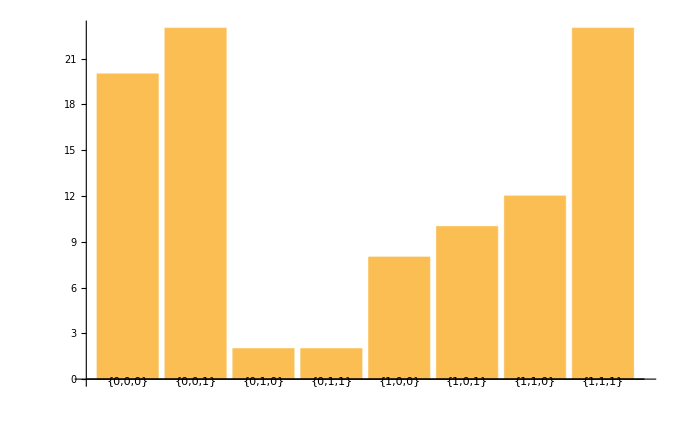

```mathematica
BarChart[KeySort@Counts@results["measurements"],ChartLabels->Automatic]
```

```mathematica
QuantumCircuitOperator[{QuantumOperator["H",{1}],QuantumOperator["CNOT",{1,2}],QuantumOperator["CNOT",{2,3}],QuantumMeasurementOperator[{1,2,3}]}][]
```

QuantumMeasurement[…]

```mathematica
QuantumCircuitOperator[{QuantumOperator["H",{1}],QuantumOperator["CNOT",{1,2}],QuantumOperator["CNOT",{2,3}]}][]==QuantumState["GHZ"]
```

True

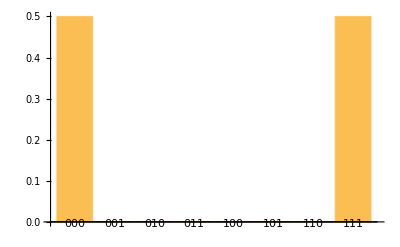

```mathematica
%["ProbabilityPlot"]
```